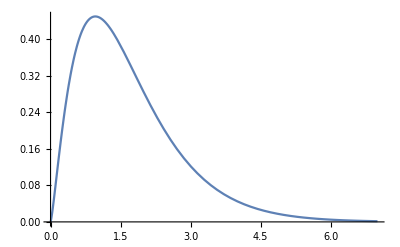

```mathematica
α = 2.321995;
β = 0.7256236;
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All]
```

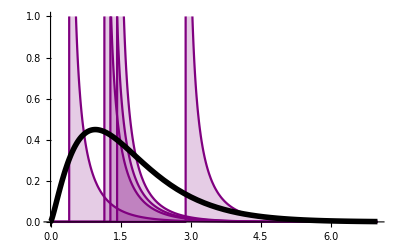

```mathematica
SeedRandom[2];
ψ = 0.1;
li = RandomVariate[GammaDistribution[(1-ψ)α,β],5];
Show[
Plot[Table[1*PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```

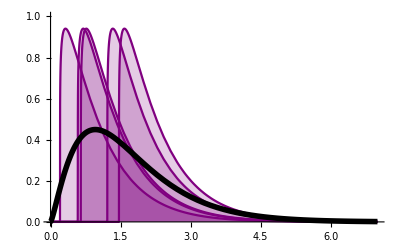

```mathematica
SeedRandom[2];
ψ = 0.5;
li = RandomVariate[GammaDistribution[(1-ψ)α,β],5];
Show[
Plot[Table[1*PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```

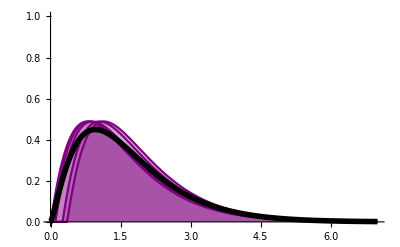

```mathematica
SeedRandom[2];
ψ = 0.9;
li = RandomVariate[GammaDistribution[(1-ψ)α,β],5];
Show[
Plot[Table[1*PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```